## γ evolution across the four fitting procedures

## Step for the MOI: 1

```mathematica
gmvalues={18,25,25,15};
```

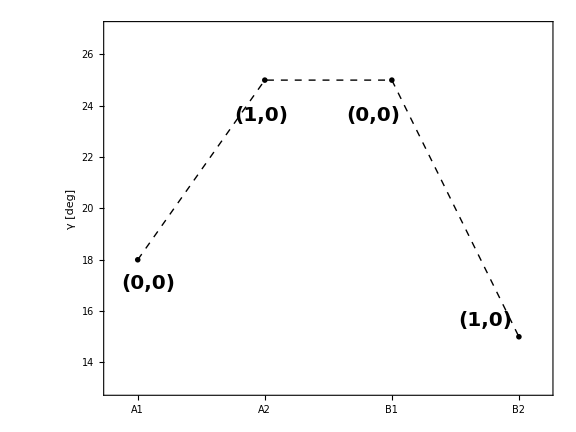

```mathematica
vPlot[values_]:=ListPlot[values,Joined->True,PlotStyle->{Thin,Dashed,Black},PlotMarkers->{ Red},AspectRatio->0.75,Frame->True,Axes->False,PlotRange->{{0.8,4.2},{13,27}},FrameStyle->Directive[Thick,Black],FrameLabel->{"","γ [deg]"},LabelStyle->{20,Black,Bold,FontFamily->"Times New Roman"},FrameTicks->{Automatic,{{{1,"A1"},{2,"A2"},{3,"B1"},{4,"B2"}},None}},Epilog->{Inset[Style["(1,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.35,0.75}]],Inset[Style["(1,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.85,0.2}]],Inset[Style["(0,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.6,0.75}]],Inset[Style["(0,0)",20,Black,Bold,FontFamily->"Times New Roman"],Scaled[{0.10,0.3}]]},ImageSize->Large];
Show[vPlot[gmvalues]]
Export["/Users/basavyr/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Unified_Model/gamma_evolution.png",Show[vPlot[gmvalues]]];
```